https://michaelberryphysics.wordpress.com/wp-content/uploads/2013/07/berry102.pdf

## Stadium

```mathematica
ClearAll[η,reg];
reg=ImplicitRegion[x<=0&&x^2+y^2==1||x>=η&&y^2+(x-η)^2==1||η≥x&&x≥0&&(y==1)||η≥x&&x≥0&&(y==-1),{x,y}];
```

```mathematica
ClearAll[arc,η];
arc[{x_,y_}]:=Which[
x>η,If[y>0,PlanarAngle[{η,0}->{{η+1,0},{x,y}}],3π/2+2η+PlanarAngle[{η,0}->{{η,-1},{x,y}}]],
0<=x<=η,If[y>0,π/2+x,3π/2+η+x],
True,π/2+η+PlanarAngle[{0,0}->{{0,1},{x,y}}]
]
```

```mathematica
ClearAll[tangent];
tangent[{px_,py_}]:=Which[
px<0,{Abs[py],-px/(Sign@py)},
px>η,{Abs[py],(-px+η)/(Sign@py)},
True,{1,0}]
```

```mathematica
ClearAll[crossing,next];
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0},{x,y}∈reg],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

```mathematica
η=.01;
α0=ArcCos[1/ⅇ];
p1=N@{η+Cos[1],Sin[1]};
p2=SortBy[crossing[p1,p1-{Sin[α0],Cos[α0]}],Norm[#-p1]&][[2]](*RandomPoint[reg]*);
```

```mathematica
bounces=10000;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
```

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

```mathematica
Manipulate[
Show[With[{pnts=DeleteDuplicates@Flatten[data,1][[;;2bn]]},ListPlot[pnts->Range[Length[pnts]],Axes->False]],Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,Line/@data[[;;bn]]}}],PlotRange->All],{bn,1,100,1}]
```

```mathematica
s=arc/@collision[[All,2]];
```

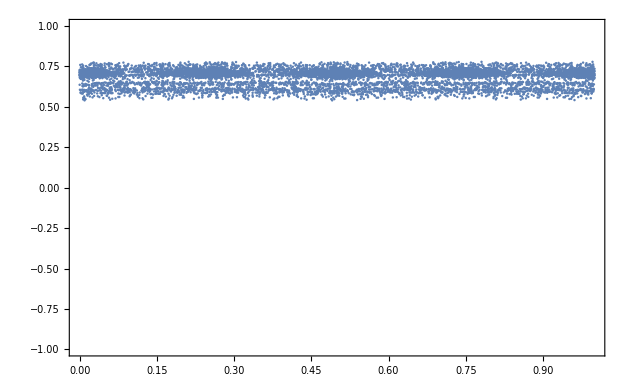

```mathematica
ListPlot[Transpose[{s/(2π+2η),Sin[θ]}],PlotRange->{{0,1},{-1,1}},Axes->False,Frame->True]
```

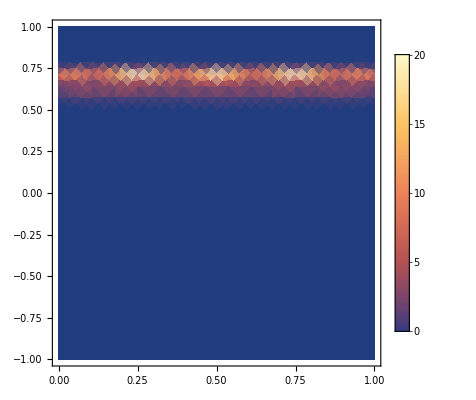

```mathematica
SmoothDensityHistogram[Transpose[{s/(2π+2η),Sin[θ]}],Automatic,"PDF",PlotLegends->Automatic,PlotRange->{{0,1},{-1,1}}]
```

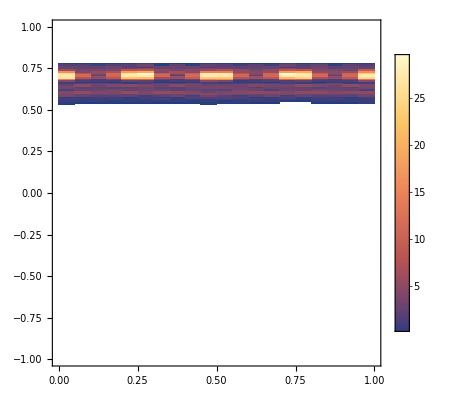

```mathematica
DensityHistogram[Transpose[{s/(2π+2η),Sin[θ]}],Automatic,"PDF",ChartLegends->Automatic,PlotRange->{{0,1},{-1,1}}]
```

## Eclipse

```mathematica
ClearAll[a,b]
a=1;b=.5;
c=√(a^2-b^2);
reg=Circle[{0,0},{a,b}];
```

```mathematica
ClearAll[tangent,crossing,next];
tangent[{px_,py_}]:=Reverse@{b^2 px,-a^2 py}
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0,x^2/a^2+y^2/b^2==1},{x,y},Reals,WorkingPrecision->MachinePrecision],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

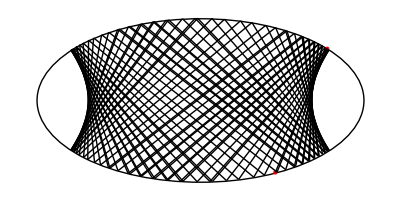

```mathematica
{p1,p2}=RandomPoint[reg,2];
bounces=100;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
Graphics[{{reg},{Red,PointSize[Large],Point[{p1,p2}]},{Line/@data}}]
```

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

```mathematica
arcAngles=With[{θ=ArcTan[b/a(#[[1]])/(#[[2]])]},If[θ>0,θ,2π+θ]]&/@collision[[All,2]];
s=ArcLength[Circle[{0,0},{a,b},{0,#}]]&/@arcAngles;
```

```mathematica
ℒ=ArcLength[Circle[{0,0},{a,b},{0,2π}]]
```

4.84422

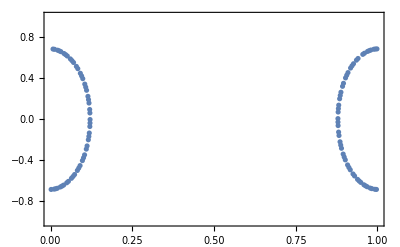

```mathematica
ListPlot[Transpose[{s/ℒ,Sin[θ]}],PlotRange->{{0,1},{-1,1}},Axes->False,Frame->True]
```